# AD_Excitation

## 1D ground state

## useful function

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};Load energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
```

## Heisenberg

#### relative error-χ

error exponentially-dependent on χ

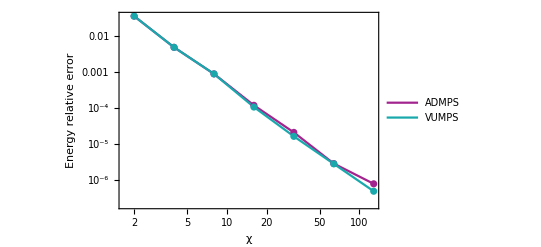

```mathematica
exact=0.25-Log[2];
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
VUMPS energy={{2,-0.4279080104197335},{4,-0.44105819788743295},{8,-0.44276214977210915},{16,-0.4431005700103215},{32,-0.443139971582285},{64,-0.4431459279483812},{128,-0.4431469616755707}};
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
VUMPS energy aberror=Table[{VUMPS energy[[i,1]],Abs[(exact-VUMPS energy[[i,2]])/exact]},{i,1,Length[VUMPS energy]}];
ListLogLogPlot[{AD MPS energy aberror,VUMPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS","VUMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

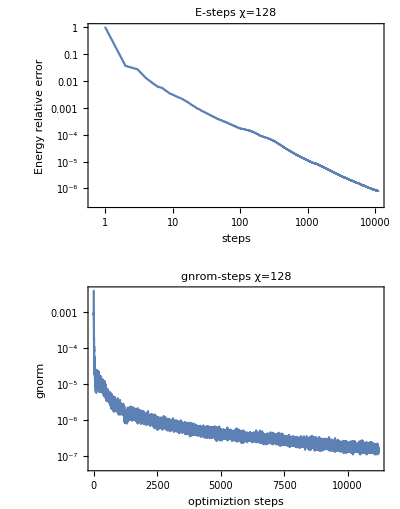

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## TFIsing at critical point g=1

#### relative error-χ

error exponentially-dependent on χ

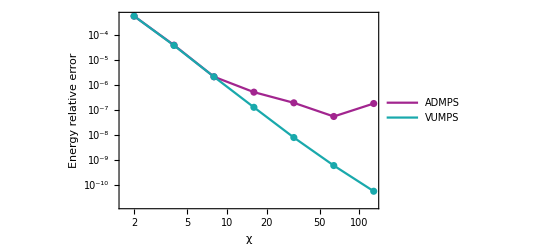

```mathematica
g=1;exact=Integrate[-1/(2Pi)Sqrt[g^2-2g Cos[k]+1],{k,0,2Pi}];
AD MPS energy={{2,-0.318135621484342},{4,-0.318297851395685},{8,-0.318309229736254},{16,-0.318309727151598},{32,-0.318309826702671},{64,-0.318309869258945},{128,-0.318309830392016}};
VUMPS energy={{2,-1.2725424859373686},{4,-1.2731927062998054},{8,-1.2732369270177255},{16,-1.273239387339872},{32,-1.2732395349825683},{64,-1.2732395439963544},{128,-1.2732395446657603}};
AD MPS energy=Table[{AD MPS energy[[i,1]],4 AD MPS energy[[i,2]]},{i,1,Length[AD MPS energy]}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
VUMPS energy aberror=Table[{VUMPS energy[[i,1]],Abs[(exact-VUMPS energy[[i,2]])/exact]},{i,1,Length[VUMPS energy]}];
ListLogLogPlot[{AD MPS energy aberror,VUMPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS","VUMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

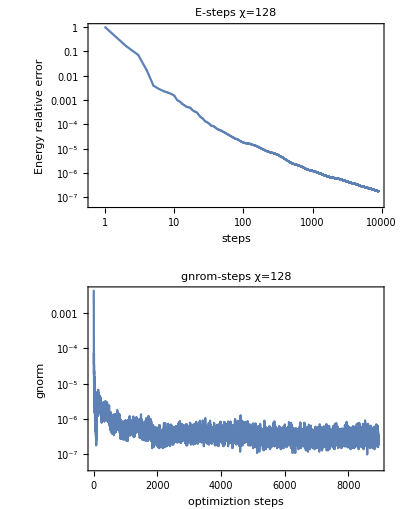

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## 1D Excitation

## U1

```mathematica
U1 = {{0.44214127746903376-0.36649815518214574I,-0.13700868205515632-0.16528649180042596I},{0.1370086836991797+0.1652864904376679I, 0.23346510468812767-0.1935230536660265I}};
U2 = {{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}
```

{{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}

```mathematica
FindRoot[Tr[Transpose[U1].U2]==0,{x,1}]
```

{x→1.5708+0.535137 ⅈ}

```mathematica
U=U2/.{x->1.5707963267948966+0.5351372028447591 ⅈ}
```

{{7.02112×10^-17-0.561047 ⅈ,-1.14664-3.43542×10^-17 ⅈ},{1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17-0.561047 ⅈ}}

```mathematica
FullSimplify[Transpose[U].U]
```

{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
ConjugateTranspose[U]
```

{{7.02112×10^-17+0.561047 ⅈ,1.14664-3.43542×10^-17 ⅈ},{-1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17+0.561047 ⅈ}}

## XXZ Δ=1

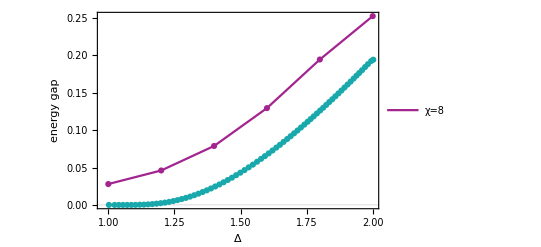

```mathematica
gap={0.05582453026702144,0.09212963838012368,0.15765165546585008,0.25902554676265305,0.38907021917034657,0.5051298373530196}/2;
energy gs=Table[{1.0+0.2(i-1),Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\XXZ{Float64}("<>ToString[NumberForm[1.0+0.2(i-1),{2,1}]]<>")\\D2_χ8.log"]},{i,1,6}];
energy gap=Table[{energy gs[[i,1]],gap[[i]]},{i,1,Length[gap]}];
Exact = Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\project\\XXZ_gap.csv"];
ListPlot[{energy gap,Exact },PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"Δ",None}},ImageSize->400]
```

## Heisenberg S=1/2

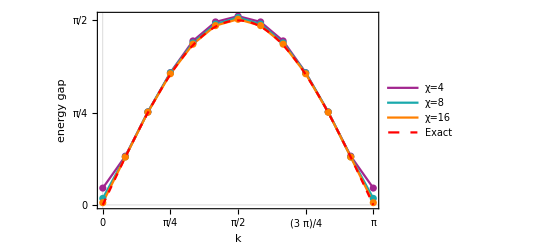

```mathematica
gap={{0.143590951236512,0.41530630963142906,0.7919144836295847,1.1263906176088896,1.3962166412387695,1.5578014262286415,1.6073219940962598,1.5578014252762273,1.3962166412329813,1.1263906186752397,0.791914483411365,0.415306313325118,0.14359095621658013},{0.055825535280367065,0.40920812813787655,0.7917343968681471,1.124766271557226,1.379519702559978,1.5398361831063736,1.5948824096077312,1.5398361216280303,1.3795198076975546,1.1247663680286026,0.791734354199969,0.40920812220705727,0.055826048730513896},{0.019355656610179933,0.40749600807271985,0.7893265909061853,1.116831940068277,1.368569477493216,1.526614821143771,1.5805417601476666,1.5266152002333788,1.3685691333818455,1.116831994201616,0.7893267774108071,0.40749554338175925,0.01936395160433102}};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,3},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=4","χ=8","χ=16"},{Scaled[{0.7,0.2}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi},PlotLegends->Placed[{"Exact"},{Scaled[{0.6,0.8}], {0, 0}}],PlotStyle->{Dashed,Red},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]}]]
```

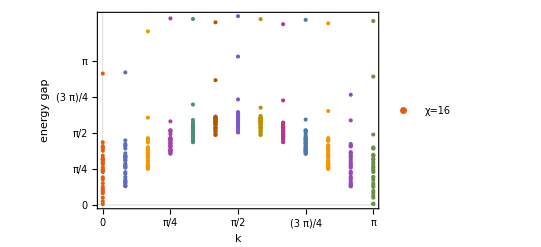

```mathematica
data={{0.019356712019114892,0.07988399537000476,0.15851980030219873,0.25463892314106706,0.287120756397108,0.30459423982442213,0.3479629943878291,0.3922590290112449,0.4730370929326074,0.5577705457747633,0.6004789242641874,0.718590070430259,0.7439289900867999,0.7495836084115252,0.7821209734141411,0.8229444507585456,0.8971681651337648,0.901995097855716,0.9439744124606408,0.9696428965384598,0.9958241788054643,1.0041003694226043,1.0054805948271819,1.0745533155732234,1.180929290460144,1.2325044004821992,1.2532894962360224,1.2837474621301057,1.3667881667284276,2.8646066019201752,},{0.40749545997731024,0.4142511021698713,0.43356413933476184,0.475406537485462,0.49283245623109206,0.5028117913747882,0.5287702964271762,0.5571428958544163,0.6106206879634741,0.6803569308483806,0.714178426296922,0.8115120209843482,0.8356798773101553,0.8374586977078984,0.8699178607399839,0.9019830647090546,0.9712917165007591,0.9737498932970463,1.0115021472245342,1.0364849155901132,1.055766434877827,1.0687115459542742,1.068754854037054,1.1253272036295503,1.2306250163019161,1.2817346376112082,1.3021807343637686,1.3300632810400672,1.4075640707087964,2.8889855941756273,},{0.7893266944597348,0.7942501629158961,0.8080983901196898,0.8329832624770432,0.8371042143663318,0.8485798469746656,0.8607240204576377,0.8770320060315122,0.8965651986306411,0.9528899687030133,0.97344525072165,1.0335063173750503,1.0485824510180348,1.0591232417233063,1.085525173213311,1.0985179256179807,1.1558025583204596,1.1603245206639765,1.1890467276198426,1.210974787432773,1.2127473679440022,1.2341645845777038,1.238221476027026,1.2593986762292515,1.3637136820530713,1.4147349287917201,1.4351944870496096,1.455853661606546,1.9035620925279053,3.7848677083057747,},{1.116831502605037,1.12476530849907,1.15430460646794,1.1687978477015146,1.1799055417539226,1.193694864650017,1.2010668235112858,1.201140538762355,1.2091965592227063,1.2590291983596569,1.2695786907497852,1.2892016469960854,1.293902273245662,1.3274472663598187,1.3388464110793226,1.351369027978242,1.3802791573229731,1.3931407515569652,1.4233732296129213,1.4258267355362826,1.4319920587187818,1.4419554188371382,1.4510467492380943,1.4647142285637693,1.5417525377787744,1.5971300132545627,1.620147193335427,1.6285552425540075,1.8219652516480467,4.066599204359205,},{1.3685689761889452,1.376751307097338,1.417512024110783,1.4435360358612712,1.4655676725300586,1.4894342455817675,1.4964296394145618,1.4989335515925373,1.5005635828143817,1.529068157428938,1.540174901301829,1.5487475185851236,1.549745216104134,1.568148444458624,1.5951481865176167,1.6000923532044522,1.6027327280920682,1.6164856580165312,1.6169190387860428,1.6699323819821772,1.6731677946889956,1.678444718734378,1.6849843360854513,1.7034394313919503,1.7217408643561687,1.763768502785001,1.7960796086984125,1.8504555137484338,2.190241957087645,4.055459789874986,},{1.5266146074808955,1.5351495579404821,1.5852007179262673,1.6093648946563477,1.636486546352942,1.6681632428651025,1.6823737812163686,1.6844391306143944,1.6847106624278922,1.7385630207524074,1.759565796077722,1.762173773125544,1.7701121016717183,1.7983222443292795,1.8105773125905387,1.8126719689438504,1.8155815421714279,1.8327868545942116,1.8381796981024656,1.8615650039854224,1.8678147252962165,1.8779402568886399,1.8924265833368583,1.8939565537326823,1.8943462671356877,1.905613231280845,1.9090383533701487,1.9254452214636193,2.72055401273043,3.9819833812412218,},{1.5805411732081112,1.5886593033410528,1.641749100020726,1.665547988944231,1.6991894622430865,1.7327092534729733,1.743381215790137,1.7497299643816298,1.7512167174567566,1.7918517854271931,1.8197636782730775,1.8212953766296298,1.825514991333764,1.8725561523658738,1.8909546742403205,1.8951320551583912,1.9045335366632057,1.9117764622737465,1.920216706315951,1.9711582067056597,1.9810155992977627,1.9947806931276375,1.9962842709797617,1.9965842909499656,2.0106626043637825,2.010819084407383,2.02378002915089,2.3005953636131786,3.235245494623999,4.116815393592645,},{1.5266146138295849,1.5337556104531076,1.585200740724084,1.6038439808725744,1.6364865104873207,1.6681635510681518,1.6823743144080967,1.6844387184175804,1.6929936377195653,1.730416462551267,1.7597857149708078,1.762173721632632,1.7701122211897062,1.7983223863939903,1.8105776141303231,1.8126718024052313,1.821274003365932,1.8327869465416147,1.8381795434754769,1.8440545833225725,1.8668261790832716,1.8779400494286325,1.8800024063408864,1.8924270460964727,1.8939575179101493,1.9056128515933148,1.9090378879259335,1.93987840005778,2.120094532159012,4.051593416680396,},{1.3685689764707742,1.3740018027016563,1.4175120848230747,1.4341878776695516,1.4655678198986097,1.489434552371823,1.4964299453534982,1.5005633268494591,1.5065077555628699,1.5135155761110382,1.5401749811009575,1.5483409819989356,1.548747165873286,1.5681498852450781,1.5951490487159559,1.6027322561778543,1.6156936862333289,1.6164862103488604,1.61691878927919,1.6633651250986146,1.6699333721222533,1.6784439961118993,1.703438341852252,1.7106140402687966,1.7136607038689378,1.7637669518331391,1.779810296957471,1.7960831218801239,2.278523198771948,3.9406181549128902,},{1.1168315115650753,1.1207256917563961,1.1543046308875105,1.160738320405532,1.1799055623809236,1.1936950195808922,1.2011408221233486,1.2091967975413735,1.2153399744747992,1.2466981314308494,1.2574855989210585,1.269577526050929,1.2892022380823884,1.327449384795426,1.3388470200992217,1.351368767498939,1.3721818850663645,1.3931413016927126,1.42337462783548,1.4258258587337995,1.4319929567168939,1.4646458055137497,1.4647136636986695,1.5074935543002541,1.5528414394724142,1.5971359155909663,1.6201469299457782,1.6285599198032636,1.8610595953487552,4.035370165640145,},{0.7893266963883178,0.7913374803738014,0.80809848355993,0.8154143044684896,0.8329832684142604,0.8485804862629531,0.8770323231891377,0.8917846288044309,0.8965655139162783,0.9466469949855978,0.9719074984729527,0.9734429173911155,1.0335067709653576,1.059123422951192,1.0855250948258277,1.0985209435743524,1.1220578572457651,1.160324874589181,1.1890460611067981,1.212751030826172,1.2382221841192163,1.2593986095342762,1.2739426924891868,1.3025837838412864,1.3957009117589567,1.4147438170082063,1.4351942444313903,1.4558556418346649,2.0483544183513422,3.9593347538821706,},{0.40749546536827774,0.40832868355849616,0.4335642927414416,0.44972609512798917,0.4754064545027773,0.5028128058092911,0.5571433015687848,0.5838917988115573,0.6106208674872218,0.6707863030727833,0.7141743390620788,0.7228397998790248,0.8115122447729578,0.8356807001116999,0.8699179445069521,0.9019865286637174,0.9212591100229373,0.9712921208859898,1.0115017943993811,1.055770828421495,1.0687574401044815,1.1253270284754826,1.1283875952837439,1.1503946181792346,1.2768589231067016,1.2817457004444024,1.3021805897405276,1.3300656037606284,1.8439581798161688,2.402502242249594,},{0.019356809950179597,0.029916300562974875,0.1585200675923619,0.1981441049937934,0.2546389233505662,0.30459575025163155,0.39225940990771535,0.43130061036785206,0.47303709405531175,0.5453999132929324,0.6004734606841438,0.6122869967014534,0.7185900761089724,0.7439301071199007,0.7821209792088036,0.8229479832735931,0.8412597973315288,0.8971684032726289,0.9439744118898505,0.9958274004267408,1.0041054365803053,1.0732846893904768,1.0745533266265916,1.0933159940135706,1.2323046279511454,1.2325162441319775,1.253289496260357,1.5347002921036776,2.7990200297345713,4.010786579441088,}};
energy gap=Table[Transpose@{Table[Pi/12 (i-1),{j,1,Length[data[[i]]]}],data[[i]]},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=16"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

## Heisenberg S=1

### energy gap err

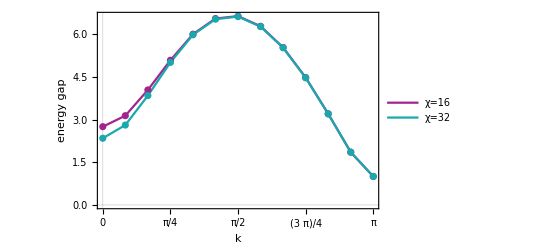

```mathematica
gap={{1.1268454257095815,1.285171785206961,1.6557565989884577,2.083020577151731,2.4584581883654395,2.6837600174326828,2.7185068607572935,2.572623823406021,2.2671755708120296,1.834096103535215,1.312574461976365,0.7600515284855315,0.4097919500865274}/0.4097919500865274,{0.9617463024620846,1.1519833989373156,1.5768092742171103,2.055853638229605,2.4543603583220612,2.67903976595536,2.7163927633731575,2.571772799105956,2.2668161567529386,1.834129470152294,1.3128049237356012,0.7604951249254354,0.4104726336238398}/0.4104726336238398};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,2},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=16","χ=32"},{Scaled[{0.7,0.2}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

### k = π energy gap error

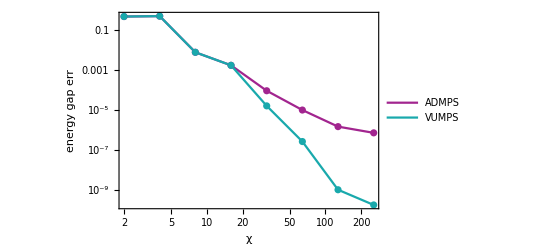

```mathematica
ADMPS={0.22222222138633316,0.2132164213483138,0.4073983283744025,0.4097915343423936,0.41044228122259074,0.410475228123841,0.41047865160632757,0.4104789568932946};
VUMPS={0.22222221626766125,0.2132164087305432,0.4073983291336687,0.4097915314728411,0.41047276288854273,0.4104791409770996,0.41047924804361297,0.4104792485361133};
Verstraete2012=0.410479248463;
ADMPS err=Table[{2^i,Abs[(ADMPS[[i]]-Verstraete2012)/Verstraete2012]},{i,1,Length[ADMPS]}];
VUMPS err=Table[{2^i,Abs[(VUMPS[[i]]-Verstraete2012)/Verstraete2012]},{i,1,Length[VUMPS]}];
Show[ListLogLogPlot[{ADMPS err,VUMPS err},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS","VUMPS"},{Scaled[{0.6,0.5}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Table[2^i,{i,1,10}],Automatic}},FrameLabel->{{"energy gap err",None},{"χ",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],PlotRange->All]
```

### excitation spectrum

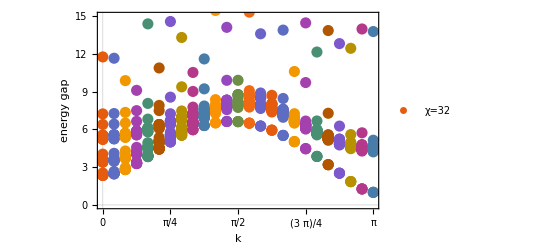

```mathematica
data={{0.9617463024619146,0.9634111720504643,0.9647352116045146,0.9800214077991101,0.9801990816546777,0.981882923125935,0.9824557903732202,0.983087168152062,1.0414864111968625,1.3931628722753235,1.398768371018499,1.40255699723393,1.4551705333279366,1.4555974429854461,1.4619227172139695,1.4643338133161279,1.466372328824409,1.6562115027948932,2.1356189921804964,2.1442160505785504,2.148077170666456,2.258543403052716,2.2591949991815543,2.26833879398281,2.2725432811247352,2.2747945436066317,2.623711551143167,2.9683187720426627,4.826674987461724,11.385963903151568,},{1.0129893524616018,1.0145778316487788,1.0158418212771387,1.0307018409684607,1.0308516312206295,1.032458067468372,1.032999437432671,1.0336018466125014,1.088826516482119,1.425954545923639,1.4314418629518197,1.4351375847045795,1.487000138976805,1.4872731313407432,1.493528979307147,1.4958913036453962,1.4978677329697154,1.6828478421753363,2.1529551920146943,2.161454106564456,2.165245672234796,2.27493075152407,2.2754256484551494,2.2845766457840537,2.2887594098128514,2.2909481772525284,2.6356945661691746,2.9802828952373814,4.783878292155997,11.554077754270518,},{1.1519833987599115,1.1533855220857243,1.1545110568494605,1.1690174198974905,1.1691565394806562,1.1705474942132437,1.1710183022055898,1.1715525515158551,1.2190596189551777,1.5189977425030432,1.5241525197378198,1.5276473325672548,1.5778435540372449,1.577978818825504,1.5838906568521258,1.586110378997359,1.5879518532917438,1.759549912022609,2.203404700747413,2.2115950436078453,2.21524602689231,2.3226369348807556,2.3230189775705106,2.331990910331933,2.3360821145846393,2.338195886074873,2.670781710060928,3.017939161777515,4.053717585320009,11.17507460704742,},{1.3487218993860755,1.3498945705126872,1.3508428014444722,1.3668489531262842,1.3669952766381754,1.3681281244387953,1.368519865582703,1.3689741850238257,1.4070208405441993,1.6591091414259838,1.663817311375894,1.6670548222276678,1.7163147757782813,1.7164053079554167,1.7217627068851296,1.723782935441969,1.7254448532285829,1.8778896184758684,2.2827009392357356,2.290414811490244,2.2938701825310703,2.3980593291145453,2.3984122131669983,2.407026022247699,2.410965362726323,2.412996354712241,2.72638161441483,3.074822212538379,3.7365090895965314,11.68449077590579,},{1.5768092743342914,1.577723175464949,1.5784677755658167,1.5994894419470984,1.5996517001541728,1.6005387629496084,1.6008582199315342,1.6012301882071975,1.6292719535667488,1.8307718006200555,1.8350096559437974,1.8379829370537906,1.8885654979771147,1.8887154916656017,1.8934030923994807,1.8952027621687448,1.8966652126128345,2.0268060126154523,2.3846397337019436,2.391767057808512,2.3949950327624143,2.495842315914869,2.4962442705712293,2.5043633493839708,2.508106273271114,2.5100496926329745,2.7987003298837902,3.3108173753531536,5.9049097402639354,11.389986909067547,},{1.8175617713348866,1.818170918218821,1.8186782011707814,1.8504122176750382,1.8505907662933483,1.8512602930176327,1.8515186068484035,1.8517993461985793,1.8692499900722563,2.0205919075152554,2.0243880167710198,2.0271243589472263,2.0818089587772337,2.0820131409462457,2.086033515168016,2.0876115388337007,2.0888674620964878,2.1951400610916845,2.5021826061208934,2.508672467474162,2.5116669375800176,2.609651585052504,2.6101345937275924,2.6176880262444437,2.6212072825718074,2.623060894842504,3.077011087074376,3.24488036518012,4.466673461210375,10.79875565671987,},{2.0558536382276755,2.0561229497047555,2.0563597364186963,2.1091499030213607,2.109341776808416,2.1098182863725636,2.110028773073764,2.110147851207202,2.1160716206130212,2.220166350691352,2.223548120897592,2.2260766355897026,2.285568230582489,2.285801323684514,2.2891931735858146,2.290554460060854,2.291596672656338,2.3731119965738925,2.6285549518204965,2.63440578841679,2.637184176657679,2.7329202798060845,2.7334852598002293,2.7404533611024102,2.743736179242064,2.7454993283350193,2.9731009917156985,3.5146866432851014,5.9812167626426405,11.490867185486087,},{2.2741098842858944,2.2741487143136316,2.2741835672853368,2.361300179860948,2.368671015554589,2.3688766819303946,2.36916371230791,2.3693147406991715,2.3696317484716163,2.4287673889747663,2.4316325055267507,2.433871185034608,2.491604020739309,2.491839296523352,2.4946415759635134,2.4957881448410717,2.4965958487280626,2.5529180369692748,2.758155925588651,2.7633988357725294,2.7659968588742005,2.859526398340002,2.8601611563756566,2.866551281250463,2.869592720960336,2.8712630447811813,3.063881263996921,3.851255821468586,5.460635352770831,11.197178769233746,},{2.454360358320965,2.4543840404735744,2.454395030258512,2.5985413869439347,2.622964656771726,2.623182709723295,2.623305560061313,2.6234282575426633,2.6235909063341483,2.6485053172530058,2.650667715736702,2.652417003312541,2.6932667954622467,2.6934753085180905,2.6957098794533754,2.696633524845122,2.6971527193583054,2.729482016091748,2.887078735226598,2.8917611959323937,2.8942291414586805,2.9846190409470337,2.985299945817023,2.9911160724643233,2.993905177407854,2.9954685533227225,3.188687633109149,3.701082620715657,4.320536649074297,12.036851668851591,},{2.58975206920159,2.5897836945213797,2.5898071913142107,2.8144196782648474,2.8634304943610798,2.863729244975937,2.8637546250405426,2.863911338870702,2.8639908935704663,2.871138535046818,2.8725731242248496,2.8737506661704284,2.8850987025210157,2.8852400781671164,2.8868939056273595,2.8875497345597743,2.887783561473166,2.9041223304287453,3.0127696956365564,3.016967862175588,3.0193931707252575,3.1069577263476256,3.1076268425411206,3.1127758957890928,3.115246496430252,3.1166343608886,3.226015981213981,3.7856773890646163,4.7611144726409975,11.89892190429484,},{2.6790397664905163,2.679057498189947,2.6790719550527466,2.9852204517340564,3.0552603232312885,3.0556485407183414,3.0561934149611654,3.056564527169519,3.056864344347792,3.0730558713732106,3.073231515687007,3.0741437849517106,3.074617272238279,3.0749048670742196,3.0807907646542843,3.081532892410048,3.081971342755789,3.0853332677400833,3.1337633995905096,3.1376659472097357,3.140303783660448,3.239537347370985,3.2400056268019846,3.243817447849093,3.2458497234350463,3.2464340583535742,3.4332837529813074,6.343201164758343,9.956660173053086,12.487350309046247,},{2.7212264691954267,2.7212351344163435,2.721240541895329,3.107129330648347,3.1954184969348436,3.195486994960258,3.196155501732453,3.196466565911473,3.196634978789054,3.2073378096264964,3.207516297442466,3.2091263436586748,3.2098516567409585,3.2104048129027136,3.22733890875448,3.2293697338000285,3.230340966304528,3.2391662727792836,3.269602250492992,3.2713418978283806,3.272791328649416,3.3748998380177477,3.4137580787460986,3.4140309594699425,3.4159619555255762,3.4170564876024603,4.063990340076408,5.791419859118088,10.178859253227996,12.481250977852618,},{2.7163927640300356,2.7163982562098195,2.716400609046903,3.1792455890604328,3.2620223674473094,3.2621612582477986,3.263577629746487,3.2642739848325517,3.2646449674031914,3.2966879230413046,3.296943916138059,3.2975096893164437,3.2980110494264165,3.298247451189833,3.307267189936181,3.309584614657509,3.3110434006416347,3.313142496323868,3.350888084568942,3.352653088498484,3.3532346741348933,3.494759236201832,3.58754115618471,3.5880129760966475,3.5932685005890126,3.5999911354530068,4.0647425312426755,7.12065523362396,10.126634180255692,12.41999381580641,},{2.6658098634748755,2.6658137561204716,2.6658155837351125,3.1909044032138816,3.271144952449515,3.2713972581104502,3.2721393220684445,3.2725609150673507,3.272803563181808,3.313285698169254,3.313657913722574,3.315068175673226,3.3159305965996326,3.3163834931622613,3.3249902534002125,3.326457928576305,3.326990694387331,3.327642616454851,3.349863577933225,3.3522636113223894,3.353727970203133,3.492833592024105,3.577215206474903,3.579121147525189,3.5798502650343664,3.6021734882817005,3.7256288297046516,6.287611723634415,9.436306987454087,12.74020811045537,},{2.571772799105757,2.5717752883029252,2.571776671176908,3.145719550279105,3.2164707347852697,3.216508208704296,3.2173629874437712,3.217795807153604,3.217974994995742,3.2511376077453824,3.2526967376858935,3.252803212501699,3.253888141911217,3.2546444394492027,3.2550167134442978,3.2642246219313518,3.2658355313467067,3.2666586803940922,3.274437653589965,3.2763155506812427,3.277150491538916,3.4798196642453756,3.4939705961066645,3.4986883300515617,3.5028518235315937,3.506034533177915,3.649962841129942,5.581309149846602,9.837271066647551,12.434819202164697,},{2.4374774843004894,2.437478851579399,2.4374796400780845,3.0303197689166304,3.082221669650467,3.0823129811886516,3.0829882228006458,3.0833340193849486,3.0835444468187756,3.107888951260275,3.109026988918651,3.1095390043391324,3.1435285220779576,3.143731836031282,3.1447339215647547,3.1452349034513585,3.1456145811745864,3.146290541559941,3.166923581505349,3.1687890539678847,3.1695344600748943,3.283395069792394,3.283935490313746,3.2889652143695085,3.292699293355435,3.305048599905127,3.574000081896712,6.572752070388685,10.224575773647366,12.638655391406111,},{2.2668161562540337,2.266816840512699,2.266817209181185,2.8586240549500235,2.901996779217088,2.902282997358292,2.9028707149843975,2.903299177434346,2.90373486944445,2.918086568942288,2.9190798474609236,2.9193096360982125,2.980189639128425,2.981578060484326,2.98230920002418,2.9829887067403775,2.983930346339275,3.013057508550751,3.01353711228419,3.0137917433010366,3.053572092055426,3.0560228161460814,3.0597748789703534,3.1068744828202264,3.1143765037325477,3.1214552720410715,3.471642782610349,5.7014329520066696,10.026576380615186,12.490701164768483,},{2.0641441776336906,2.0641445257976425,2.064144702527962,2.6684245155686526,2.7055915610626307,2.7061613227237302,2.7067428372792,2.7074130041284157,2.708181057170038,2.718958440917611,2.7198239063491942,2.7199470812839617,2.781268979011055,2.783420534229102,2.784639503724176,2.785096320036578,2.7864652041862277,2.8250995038808373,2.8271435356483368,2.8285051176062956,2.8315311157824934,2.832462627547908,2.8370877084787867,2.8390751927792266,2.9751679320362543,4.351340360709907,7.007336481391929,8.675739873275397,11.652265069162691,12.795436947741113,},{1.8341294704002968,1.8341296577092596,1.834129754824068,2.474384720058946,2.5064379389264606,2.5072707852578646,2.5078842690844927,2.5088279619341285,2.5099646225337073,2.5196675508661888,2.5202397448418825,2.5206752093797777,2.5761374264307837,2.5787916951505836,2.5804267495259414,2.58092261168471,2.582587395431135,2.614245552703265,2.615475174963742,2.6213756037404914,2.6232856335822152,2.6252207036453394,2.628822278113442,2.6298879944842666,2.735131590474417,3.9909012773218815,5.93678353535383,9.49651825028107,11.64471596123229,12.80608722916354,},{1.5817805600777686,1.58178065669844,1.581780701409708,2.2851951950002687,2.3135217050515458,2.314574539329349,2.3152595091593082,2.316457947584546,2.317959859263188,2.3276099590341857,2.3279049342661895,2.328672878986461,2.3787947683358026,2.381829422264477,2.38384163396442,2.3844150499355425,2.386351325030037,2.411510564278512,2.4128599165712203,2.4193649770749768,2.421824844978753,2.4237575513984715,2.427768642994857,2.428262485915399,2.449509418470414,2.453490686471057,2.737581092061155,4.9863266779191004,9.779664275104922,12.730031537513458,},{1.3128049238993265,1.3128049895476541,1.3128050057557654,2.109244032005525,2.1352864834819463,2.1365217311424054,2.1373077375281717,2.1387331654757995,2.1405767753401213,2.150596361870563,2.1506757231403784,2.1517425590979737,2.1984179056557758,2.201769446878622,2.204148634979665,2.2048073379573543,2.2070031880787613,2.228598686369571,2.2301248433674057,2.2372156378185086,2.240137753171743,2.242193133808525,2.246683548570308,2.2471637959318116,2.2819547538737663,2.286588615501499,2.9896722576874217,5.6869640714929055,9.297841418272986,12.376168268062253,},{1.0347343337166237,1.0347343591592113,1.0347343753085587,1.9558865428498016,1.9808874379295203,1.9822750132276548,1.9831753318944088,1.984797574674249,1.9869456054184544,1.9973649652765155,1.9975534806538957,1.998739438570774,2.043799063931974,2.0474321604619234,2.0501591762145472,2.050913336062329,2.053349384548932,2.073110910439764,2.0748100375128486,2.082489502366838,2.0858499156294275,2.088051747569318,2.093030663401718,2.093494890288238,2.1435572816133655,2.148241568679897,2.571194608775463,5.260894756848693,9.234880406117167,12.364480084092486,},{0.7604951249262425,0.7604951853227809,0.7604952509222765,1.8354206357511273,1.8602340110051403,1.8617436287520976,1.862752715268504,1.864532677754285,1.8669298537048546,1.8777525209317214,1.8781031189587414,1.879348660141124,1.924067003365862,1.927942841365594,1.9309717269391453,1.9318222871257242,1.9344625763826133,1.9534054190439947,1.955245215741133,1.963470984665419,1.9672183515899548,1.9695594732178963,1.9749889442290625,1.9754373916531793,2.029273466908334,2.0348033019020586,2.2933848691959526,5.107393680603831,9.63974760794753,12.480791098942893,},{0.521828141617232,0.5218281558405691,0.5218281689163934,1.7579413499605407,1.7829328826329407,1.784524765633977,1.785615695370341,1.7874984155355451,1.790063488644265,1.801200201837778,1.8016668834521892,1.8029452164657582,1.847876894542901,1.8519245084884965,1.8551648857361054,1.856095965611129,1.8588764169341652,1.8775298387859352,1.879452070702898,1.8880876205509214,1.892114935865698,1.8945559178033287,1.900312819786122,1.9007493732386138,1.9597480855985212,1.9655469733706643,2.351973137703426,5.737980667788239,8.751547130316414,12.648828724089219,},{0.4104726336240609,0.4104726658366895,0.41047268769719064,1.7311450421202206,1.7562515723762013,1.7578726369511029,1.7589996264246266,1.7609138029637081,1.7635390580342263,1.7747920829763155,1.7753121282526552,1.776591511881077,1.8216773436633356,1.82578536191422,1.8290993869148258,1.8300787503424467,1.8329065807643938,1.851488600401255,1.853414239083825,1.8622239035053312,1.866366158157599,1.868839183859757,1.8747170615087065,1.8751456361235521,1.935926936662179,1.941890019463849,2.110361066154903,5.654366677447439,9.62401830936592,12.56468472048587,}};
energy gap=Table[Transpose@{Table[Pi/24 (i-1),{j,1,Length[data[[i]]]}],data[[i]]/0.41047263362385233},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->{{0,Pi},{0,15}},PlotStyle->PointSize[0.02],Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=32"},{Scaled[{0.5,0.0}], {0, 0}}],FrameTicks->{{Automatic,All},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

PHYSICAL REVIEW B 85, 100408(R) (2012) Fig.3

## TFIsing

### energy gap

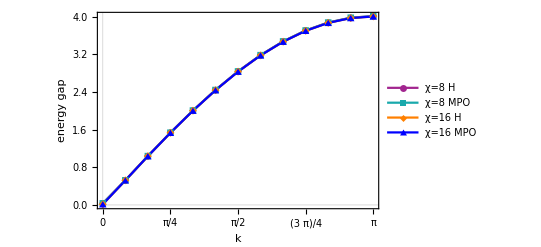

```mathematica
gap={{0.034022792873180926,0.5233769992999212,1.0379610052154,1.5350862712443503,2.0059126816509276,2.4424519254256736,2.8370662558980095,3.1831731045873526,3.4747910281056074,3.7069507410048073,3.875705781700252,3.978095406210058,4.012394495568416},{0.034022793067079116,0.5233769993260422,1.037961005295828,1.5350862712449884,2.0059126816284096,2.4424519254655186,2.8370662559308,3.1831731045300726,3.474791028051811,3.7069507409084785,3.875705781468054,3.9780954057498352,4.012394495101527},{0.014135334554457127,0.5225738586085501,1.0365103551668577,1.5326825725533066,2.0025759745624385,2.438224392466987,2.8321350528115534,3.1775901453026028,3.46867340512325,3.7003995945454173,3.868813418303316,3.971028471716269,4.0052935611326355},{0.014135329655954543,0.5225738618817211,1.0365103580745032,1.5326825745190384,2.002575974822417,2.4382243934789765,2.832135054488127,3.1775901470636856,3.4686734068596285,3.7003995952788986,3.868813418877597,3.971028473075072,4.005293562298034}};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,Length[gap]},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8 H","χ=8 MPO","χ=16 H","χ=16 MPO"},{Scaled[{0.55,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

## 2D cylinder ground state

## Heisenberg

#### relative error-χ

error exponentially-dependent on χ

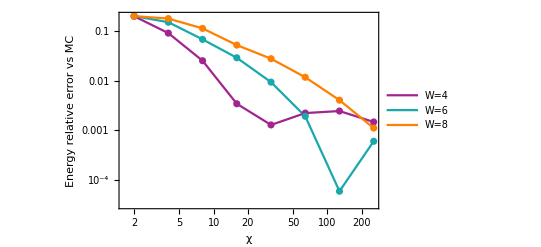

```mathematica
MC=-0.6694421;
VUMPS energy={{{2,-0.5807255723395672},{4,-0.6289009820451575},{8,-0.6581827324605429},{16,-0.6679116436055048},{32,-0.6700152111990748},{64,-0.6704352655820109},{128,-0.6705342801603063},{256,-0.6700990777644238}},{{2,-0.5802863569122595},{4,-0.6021683170351049},{8,-0.6391081626332298},{16,-0.6565218813985303},{32,-0.6652711591695919},{64,-0.6685860562665449},{128,-0.6694685551529367},{256,-0.6697103943816338}},{{2,-0.5802856246676891},{4,-0.5898604035239774},{8,-0.618971358062268},{16,-0.6461842419580633},{32,-0.6570632874826308},{64,-0.6642083711260656},{128,-0.6676357939156123},{256,-0.6689463786573655}}};
VUMPS energy aberror=Table[Table[{VUMPS energy[[j,i,1]],Abs[(MC-VUMPS energy[[j,i,2]])/exact]},{i,1,Length[VUMPS energy[[j]]]}],{j,1,Length[VUMPS energy]}];
ListLogLogPlot[VUMPS energy aberror,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"W=4","W=6","W=8"},{Scaled[{0.8,0.6}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Table[2^i,{i,1,10}],Automatic}},FrameLabel->{{"Energy relative error vs MC",None},{HoldForm["χ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
```

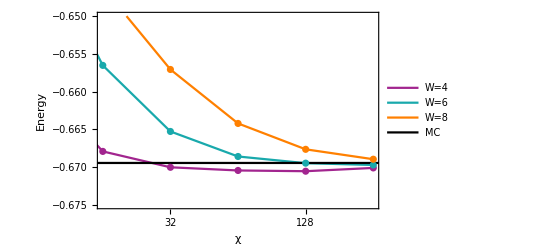

```mathematica
MC=-0.6694421;
VUMPS energy={{{2,-0.5807255723395672},{4,-0.6289009820451575},{8,-0.6581827324605429},{16,-0.6679116436055048},{32,-0.6700152111990748},{64,-0.6704352655820109},{128,-0.670534280154629},{256,-0.6700990777644238}},{{2,-0.5802863569122595},{4,-0.6021683170351049},{8,-0.6391081626332298},{16,-0.6565218813985303},{32,-0.6652711591695919},{64,-0.6685860562665449},{128,-0.6694685551529367},{256,-0.6697103943816338}},{{2,-0.5802856246676891},{4,-0.5898604035239774},{8,-0.618971358062268},{16,-0.6461842419580633},{32,-0.6570632874826308},{64,-0.6642083711260656},{128,-0.6676357939156123},{256,-0.6689463786573655}},{{1,MC},{512,MC}}};
VUMPS energy=Table[Table[{Log[2,VUMPS energy[[j,i,1]]],VUMPS energy[[j,i,2]]},{i,1,Length[VUMPS energy[[j]]]}],{j,1,Length[VUMPS energy]}];
ListPlot[VUMPS energy,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Black},PlotLegends->Placed[{"W=4","W=6","W=8","MC"},{Scaled[{0.7,0.4}], {0, 0}}],Joined->{True,True},Mesh->All,PlotRange->{{4,8},{-0.675,-0.65}},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Table[{i,2^i},{i,1,10}],Automatic}},FrameLabel->{{"Energy",None},{HoldForm["χ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
```